```mathematica
GN1gauss[q_, p_, z_, r_] = (Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}])* (Sum[PDF[PoissonDistribution[z],k]*Sum[PDF[BinomialDistribution[k,p],w]*CDF[NormalDistribution[r,0.2],w/k], {w, 0, k}],{k,1,100}]);
```

```mathematica
CascadeNode2[z_, r_] = (SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],0]*SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],2]);
```

```mathematica
data=BinaryReadList["~/Documents/BT_MP/BT_MP/coordination_game/simulations/pp_node_swap_sim_100_com.dat","Real32"];
```

```mathematica
griddat = ArrayReshape[data, {20, 21}];
```

```mathematica
zcoord = Range[0.5, 10, 0.5];
```

```mathematica
rcoord = Range[0, 0.4, 0.02];
```

```mathematica
Flatten[Table[{rcoord[[j]],zcoord[[i]],griddat[[i,j]]},{j,21},{i,20}],1];
```

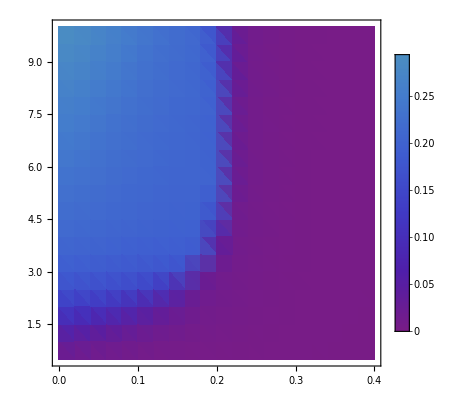

```mathematica
ListDensityPlot[%105, ColorFunction->"Rainbow", ColorFunctionScaling->False, PlotLegends -> Automatic]
```

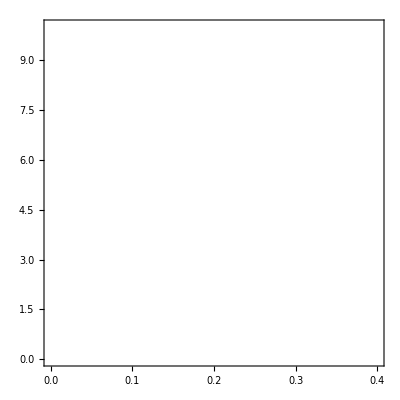

```mathematica
ContourPlot[CascadeNode2[z,r]==0,{r,0,0.4},{z,0,10},ContourStyle->Directive[RGBColor[1.,1.,1.],Opacity[0.4]]]
```

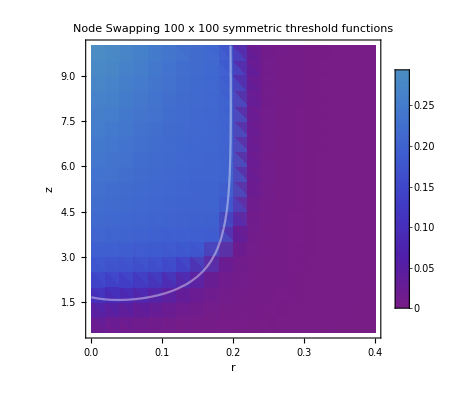

```mathematica
Show[%117, %110, AxesLabel->{r,z}, FrameLabel->{{HoldForm[z],None},{HoldForm[r],None}},PlotLabel->HoldForm[Node Swapping 100x 100 symmetric threshold functions],LabelStyle->{GrayLevel[0]}]
```